# Training COMPNANO

## Part 1 : The Si atom

Let’s analyze the results

```mathematica
wrkdir="/home/qap/wrk/part1_si_atom";
SetDirectory[wrkdir];
```

```mathematica
data1=Import["cell1.dat"];
data1//TableForm
```

4. | 0.682733
5. | 0.314779
6. | 0.0478774
7. | -0.0821503
8. | -0.134513
9. | -0.153972
10. | -0.160893
11. | -0.163275
12. | -0.164071

The following data was obtained with spin polarization in VASP (ISPIN=2)

```mathematica
data2=Import["cell.dat"];

data2//TableForm
```

4. | -0.187866
5. | -0.48054
6. | -0.706737
7. | -0.81688
8. | -0.860128
9. | -0.876064
10. | -0.881248
11. | -0.882767
12. | -0.883632
4. | -0.187866
5. | -0.48054
6. | -0.706737
7. | -0.81688
8. | -0.860128
9. | -0.876064
10. | -0.881248
11. | -0.882767
12. | -0.883632

```mathematica
{data1,data2}//ListLinePlot[#,
Mesh->Full,
PlotMarkers->{Automatic,8},
Frame->True,
FrameLabel->{"Cell Length (Å)", "Energy (eV)"},
Axes->False,
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
PlotStyle->{{Red,Thick},{Blue,Thick}},
InterpolationOrder->2,
ImageSize->400,
Epilog->{
Inset[
Panel[
Grid[{{"•","■"},{"ISPIN=1", "ISPIN=2"}}//Transpose//Map[Style[#,18]&,#,{2}]&]],{Right,Top},{1.2,1.3}]}]&
```

-Graphics-

HERE PUT DISCUSSIONS

## Part 2: The Cl^- ion

Let’s analyze the results

```mathematica
wrkdir="/home/qap/wrk/part2_cl_ion";
SetDirectory[wrkdir];
```

```mathematica
data1=Import["cell1.dat"];
data1//TableForm
```

4. | -2.52237
6. | -5.82899
8. | -5.93543
10. | -5.72528
12. | -5.51188
14. | -5.33305
16. | -5.18736

```mathematica
data2=Import["cell.dat","Table"];
data2//TableForm
```

4. | -0.87907
6. | -3.65645
8. | -3.9341
10. | -3.97215
12. | -3.979
14. | -3.98139
16. | -3.98288

```mathematica
{data1,data2}//ListLinePlot[#,
Mesh->Full,
PlotMarkers->{Automatic,8},
Frame->True,
FrameLabel->{"Cell Length (Å)", "Energy (eV)"},
Axes->False,
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
PlotStyle->{{Red,Thick},{Blue,Thick}},
InterpolationOrder->1,
ImageSize->400,
Epilog->{Inset[
Panel[
Grid[{{"•","■"},{"No IDIPOL", "IDIPOL=4"}}//Transpose//Map[Style[#,18]&,#,{2}]&]],{Right,Top},{1.2,1.3}]}]&
```

-Graphics-

```mathematica
data1=Import["/home/qap/wrk/part2_cl_ion/cell.dat"];
data1//TableForm
```

4. | -0.87907
6. | -3.65645
8. | -3.9341
10. | -3.97215
12. | -3.979
14. | -3.98139
16. | -3.98288

```mathematica
data2=Import["/home/qap/wrk/part2_cl_ion/cell1.dat"];
data2//TableForm
```

4. | -2.52237
6. | -5.82899
8. | -5.93543
10. | -5.72528
12. | -5.51188
14. | -5.33305
16. | -5.18736

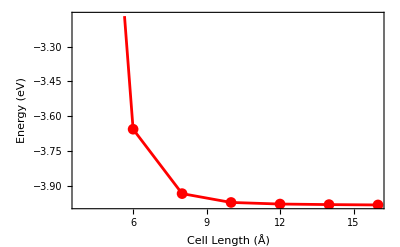

```mathematica
ListLinePlot[data2,PlotMarkers->Automatic,
BaseStyle->{FontFamily->"Helvetica"},
PlotStyle->{{Red,PointSize[Large]},{Blue,Thick}},
Frame->True,
FrameLabel->{"Cell Length (Å)","Energy (eV)"}]
```

```mathematica
{data2,data1}//ListLinePlot[#,
Mesh->Full,
PlotMarkers->{Automatic,8},
Frame->True,
FrameLabel->{"Cell Length (Å)","Energy (eV)"},
Axes->False,
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
PlotStyle->{{Red,Thick},{Blue,Thick}},
InterpolationOrder->2,
ImageSize->400,
Epilog->{
Inset[
Panel[
Grid[{{"•","◼"},{"No IDIPOL","ISPIN=4"}}//Transpose//Map[Style[#,18]&,#,{2}]&]
],{Right,Top},{1.2,1.3}]}
]&
```

-Graphics-

## Part 3 : The Silicon Crystal

```mathematica
wrkdir="/home/qap/wrk/part3_silicon";
SetDirectory[wrkdir];
```

### Analysis of the ENCUT

```mathematica
datasi=Import["ecut.dat"]//Map[#/{1,2}&,#]&
```

Thread::tdlen: Objects of unequal length in {200} {1,1/2} cannot be combined.

Thread::tdlen: Objects of unequal length in {250} {1,1/2} cannot be combined.

Thread::tdlen: Objects of unequal length in {300} {1,1/2} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

{{200,-5.43008},{250,-5.4322},{300,-5.43243},{350,-5.43255},{400,-5.43263},{450,-5.43268},{500,-5.43274},{550,-5.43278},{600,-5.43279},{650,-5.4328},{700,-5.43281},{750,-5.43283},{800,-5.43284},{850,-5.43284},{200} {1,1/2},{250} {1,1/2},{300} {1,1/2},{350} {1,1/2},{400,-5.43291},{450,-5.43296},{500,-5.43302},{550,-5.43306},{600,-5.43307},{650,-5.43308},{700,-5.43309},{750,-5.43311},{800,-5.43312},{850,-5.43312},{900,-5.43312},{200} {1,1/2},{250} {1,1/2},{300} {1,1/2},{350} {1,1/2},{400,-5.43291},{450,-5.43296},{500,-5.43302},{550,-5.43306},{600,-5.43307},{650,-5.43308},{700,-5.43309},{750,-5.43311},{800,-5.43312},{850,-5.43312},{900,-5.43312}}

```mathematica
datasi//ListPlot[#,
Frame->True,
FrameLabel->{"E_cut (eV)", "Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->500,
Epilog->{Red,AbsolutePointSize[5], Point[#]}]&
```

-Graphics-

### Analysis of k - points

```mathematica
datakp=Import["kps.dat"]//Map[#/{1,2}&,#]&
```

{{3,-5.13186},{4,-5.34158},{5,-5.4016},{6,-5.42124},{7,-5.42824},{8,-5.43091},{9,-5.43198},{10,-5.43244},{11,-5.43262},{12,-5.43272}}

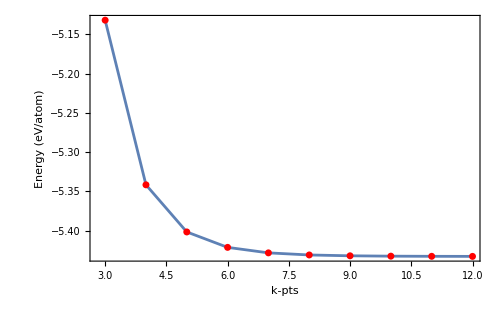

```mathematica
datakp//ListPlot[#,
Frame->True,
FrameLabel->{"k-pts","Energy (eV/atom)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->500,
Epilog->{Red,AbsolutePointSize[5],Point[#]}]&
```

```mathematica
cell=Import["cell.dat"]//Map[{1/4 (#[[1]])^3,#[[2]]}&,#]&
```

{{38.7135,-10.8397},{39.1477,-10.8507},{39.5851,-10.8587},{40.0258,-10.8637},{40.2473,-10.8652},{40.4697,-10.8659},{40.6928,-10.866},{40.9168,-10.8654},{41.1416,-10.8642},{41.3673,-10.8623},{41.821,-10.8566},{42.2781,-10.8485},{42.7385,-10.838}}

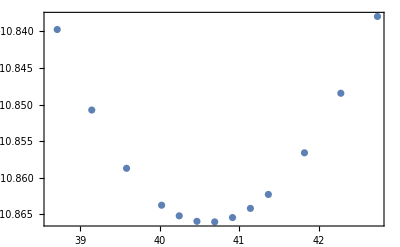

```mathematica
cell//ListPlot[#,Frame->True]&
```

```mathematica
eos=e0+(9 v0 B0)/16(((v0/v)^(2/3)-1)^3 B0'+((v0/v)^(2/3)-1)^2 (6-4 (v0/v)^(2/3)))
```

e0+9/16 B0 v0 ((6-4 (v0/v)^(2/3)) (-1+(v0/v)^(2/3))^2+(-1+(v0/v)^(2/3))^3 B0')

```mathematica
eos//PowerExpand//ExpandAll//Collect[#,v]&
```

e0+(27 B0 v0)/8-9/16 B0 v0 B0'+(-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)+(-(9 B0 v0^3)/4+9/16 B0 v0^3 B0')/v^2

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
parameters=Table[k[i],{i,4}];
nlm=NonlinearModelFit[cell,model,parameters,v]
```

FittedModel[…]

```mathematica
nlm[v]//Normal
```

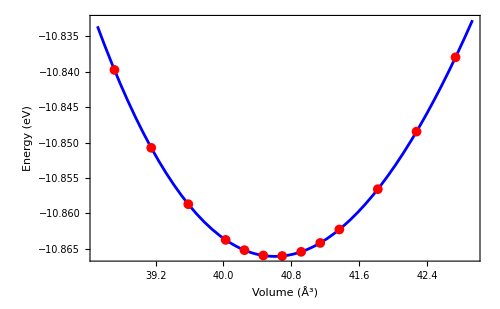

```mathematica
Plot[nlm[v],{v,(cell[[All,1]]//Min)-0.2, (cell[[All,1]]//Max)+0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)", "Energy (eV)"},
PlotStyle->{AbsoluteThickness[2], Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cell]}]
```

```mathematica
optVol=FindMinimum[nlm//Normal,{v,39.43}]
```

{-10.8661,{v→40.6055}}

```mathematica
Solve[vol==s^3/4,s]
```

{{s→(-2)^(2/3) vol^(1/3)},{s→2^(2/3) vol^(1/3)},{s→-(-1)^(1/3) 2^(2/3) vol^(1/3)}}

```mathematica
2^(2/3) v^(1/3)/.optVol[[2]]
```

5.45609

The bulk modulus B_0 is:

```mathematica
bulkm=v D[nlm//Normal,{v,2}]/.optVol[[2]]
```

0.549041

```mathematica
v D[nlm//Normal,{v,2}]/.optVol[[2]]//UnitConvert[Quantity[#,"Electronvolts"/("Angstroms")^3],"GigaPascals"]&
```

87.966 GPa

```mathematica
-v/bulkm D[v D[nlm//Normal,{v,2}],v]/.optVol[[2]]
```

4.28747

```mathematica
sol=Solve[{
e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],
63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],
-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm["BestFitParameters"],{e0,B0,B',v0}]
```

{{e0→-10.8661,B0→0.549041,B'→4.28747,v0→40.6055}}

```mathematica
(vcal-vexp)/vexp 100/.{vexp->5.429,vcal->5.403244142702353}
```

-0.474413

## Part 4 : The silicon crystal, functionals

```mathematica
wrkdir="/home/qap/wrk/part4_silicon2";
SetDirectory[wrkdir];
```

### Results using PAW - PBE

```mathematica
cell=Import["cell-pbe.dat"]//Map[{1/4 (#[[1]])^3,#[[2]]}&,#]&
```

{{39.366,-10.8249},{39.805,-10.8335},{40.2473,-10.8392},{40.4697,-10.8409},{40.6928,-10.8419},{40.9168,-10.8421},{41.1416,-10.8419},{41.3673,-10.8409},{41.5938,-10.8392},{42.0492,-10.8337},{42.5079,-10.8259}}

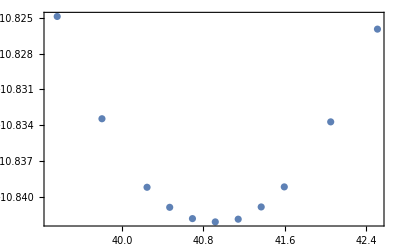

```mathematica
cell//ListPlot[#,Frame->True]&
```

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
parameters=Table[k[i],{i,4}];
nlm=NonlinearModelFit[cell,model,parameters,v]
```

FittedModel[…]

```mathematica
nlm[v]//Normal
```

13.8138+1739.6/v^2+3182.6/v^(4/3)-573.135/v^(2/3)

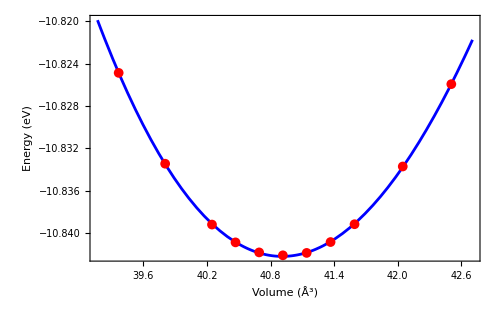

```mathematica
Plot[nlm[v],{v,(cell[[All,1]]//Min)-0.2, (cell[[All,1]]//Max)+0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)", "Energy (eV)"},
PlotStyle->{AbsoluteThickness[2], Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cell]}]
```

```mathematica
sol=Solve[{
e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],
63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],
-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm["BestFitParameters"],{e0,B0,B',v0}]
```

{{e0→-10.8422,B0→0.558301,B'→4.0809,v0→40.9105}}

```mathematica
optVol=FindMinimum[nlm//Normal,{v,40.8915}]
```

{-10.8422,{v→40.9105}}

```mathematica
2^(2/3) v0^(1/3)/.sol[[1]]
```

5.46972

```mathematica
B0/.sol[[1]]
```

0.558301

```mathematica
B0/.sol[[1]]//UnitConvert[Quantity[#,"Electronvolts"/("Angstroms")^3],"GigaPascals"]&
```

89.4497 GPa

```mathematica
(vcal-vexp)/vexp 100/.{vexp->5.429,vcal->5.468870694642815}
```

0.734402

```mathematica
(bcal-bexp)/bexp 100/.{bexp->98,bcal->89.}
```

-9.18367

### Results using PAW - PBEsol

```mathematica
cell=Import["cell-lda.dat"]//Map[{1/4 (#[[1]])^3,#[[2]]}&,#]&
```

{{37.8549,-11.8892},{38.2826,-11.8994},{38.7135,-11.9061},{38.9302,-11.9085},{39.1477,-11.91},{39.366,-11.9106},{39.5851,-11.9107},{39.805,-11.9098},{40.0258,-11.9084},{40.4697,-11.9033},{40.9168,-11.8954}}

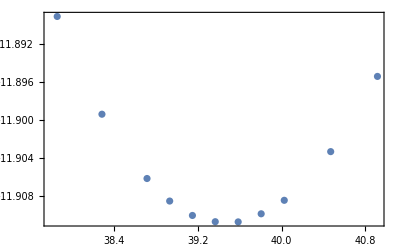

```mathematica
cell//ListPlot[#,Frame->True]&
```

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
parameters=Table[k[i],{i,4}];
nlm=NonlinearModelFit[cell,model,parameters,v]
```

FittedModel[…]

```mathematica
nlm[v]
```

13.9876+1875.87/v^2+3156.35/v^(4/3)-586.461/v^(2/3)

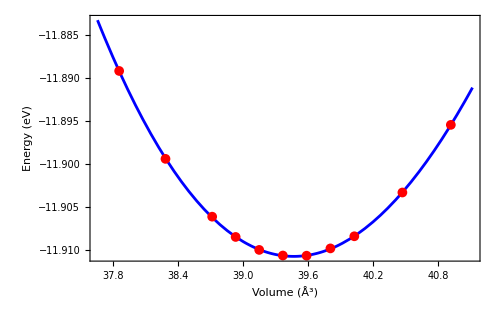

```mathematica
Plot[nlm[v],{v,(cell[[All,1]]//Min)-0.2, (cell[[All,1]]//Max)+0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)", "Energy (eV)"},
PlotStyle->{AbsoluteThickness[2], Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cell]}]
```

```mathematica
sol=Solve[{
e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],
63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],
-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm["BestFitParameters"],{e0,B0,B',v0}]
```

{{e0→-11.9107,B0→0.610421,B'→4.08887,v0→39.4667}}

```mathematica
2^(2/3) v0^(1/3)/.sol[[1]]
```

5.4046

```mathematica
B0/.sol[[1]]//UnitConvert[Quantity[#,"Electronvolts"/("Angstroms")^3],"GigaPascals"]&
```

97.8002 GPa

## Part 5 : The silicon crystal using PBE

```mathematica
wrkdir="/home/qap/wrk/part5_silicon3";
SetDirectory[wrkdir];
```

```mathematica
input=Import["DOSCAR", "Table"];
```

```mathematica
input;
```

```mathematica
dos=input[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input[[6,4]]
```

5.66802

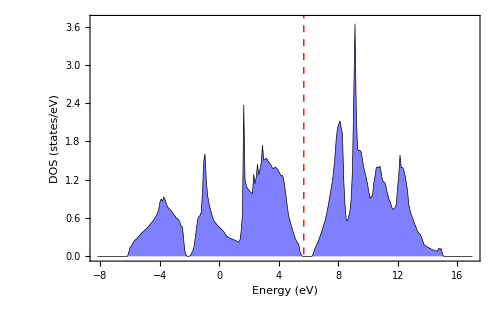

```mathematica
ListPlot[dos,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)", "DOS (states/eV)"},
GridLines->{{ef}, None},
GridLinesStyle->Directive[Red, Dashed, AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->{All, {0,3.7}}]
```

```mathematica
interp=Interpolation[dos]
```

InterpolatingFunction[…]

```mathematica
NIntegrate[interp[x],{x,-8,ef}]
```

8.05696

Here we are going to analyze de PDOS, the arrange of the data PDOS is according to the AO:
energy,  s,  p_y p_z p_x d_{xy} d_{yz} d_{z2-r2} d_{xz} d_{x2-y2}

```mathematica
dos1=input[[7+300+2;;7+300+2+300]];
dos2=input[[7+300+2+300+2;;7+300+2+300+2+300]];
```

```mathematica
dosall=(dos1+dos2)//Map[#/{2,1,1,1,1,1,1,1,1,1}&,#]&;
```

```mathematica
f[total]=Map[{#[[1]],Plus@@(#[[2;;10]])}&,#]&;
f[s]=Map[{#[[1]],#[[2]]}&,#]&;
f[p]=Map[{#[[1]],Plus@@(#[[3;;5]])}&,#]&;
f[d]=Map[{#[[1]],Plus@@(#[[6;;10]])}&,#]&;
f[py]=Map[{#[[1]],#[[3]]}&,#]&;
f[pz]=Map[{#[[1]],#[[4]]}&,#]&;
f[px]=Map[{#[[1]],#[[5]]}&,#]&;
```

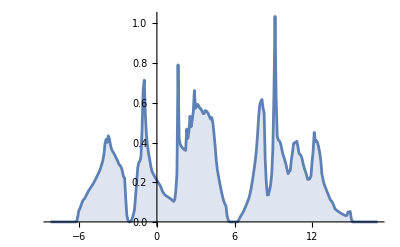

```mathematica
dosall//f[total]//ListPlot[#,Joined->True,Filling->Axis]&
```

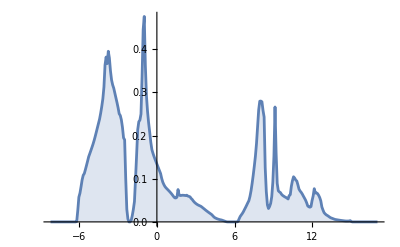

```mathematica
dosall//f[s]//ListPlot[#,Joined->True,Filling->Axis]&
```

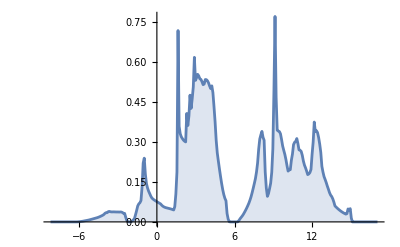

```mathematica
dosall//f[p]//ListPlot[#,Joined->True,Filling->Axis]&
```

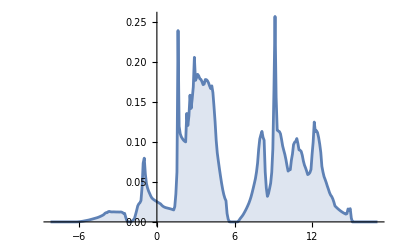

```mathematica
dosall//f[py]//ListPlot[#,Joined->True,Filling->Axis]&
```

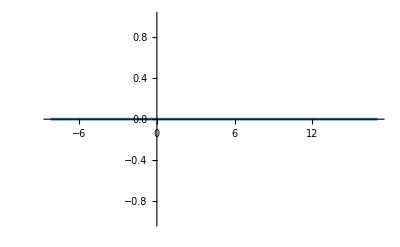

```mathematica
dosall//f[d]//ListPlot[#,Joined->True,Filling->Axis]&
```

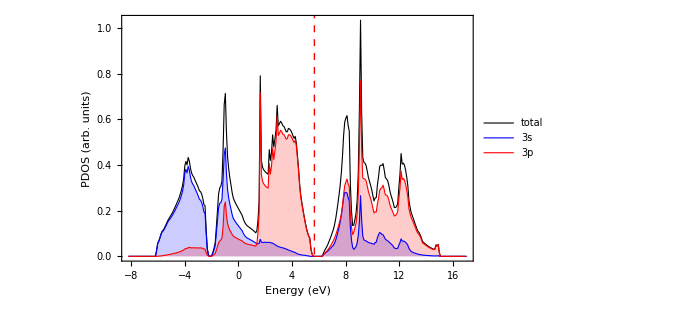

```mathematica
{dosall//f[total],dosall//f[s], dosall//f[p] }//ListPlot[#,
Joined->True,
GridLines->{{ef},None},
Filling->{2->Axis,3->Axis},
Frame->True,
PlotRange->All,
PlotLegends->Placed[{"total", "3s", "3p"}, {Scaled[{0,0.75}],{0,0.5}}],
ImageSize->500,
Axes->None,
GridLinesStyle->Directive[Red, Dashed, AbsoluteThickness[1.0]],
PlotStyle->{{AbsoluteThickness[0.8], Black}, {AbsoluteThickness[0.8], Blue}, {AbsoluteThickness[0.8], Red}},
FrameLabel->{"Energy (eV)", "PDOS (arb. units)"},
BaseStyle->{FontFamily->"Helvetica", FontSize->18}]&
```

### Visualization of CHGCAR.vasp

In the following image we display the iso-density of the valence electrons, notice the distribution

```mathematica
-Graphics-;
```

In the following image we display the contour plot of the electronic density

```mathematica
-Graphics-;
```

## Part 6 : The silicon crystal phases

```mathematica
wrkdir=wrkdir="/home/qap/wrk/part6_silicon4/results";
SetDirectory[wrkdir];
```

### The ENCUT

We are going to study the behaviour of ENCUT VS the total energy/atom

```mathematica
datasi=Import["ecut.dat"]//Map[#/{1,2}&,#]&
```

{{250,-5.11848},{300,-5.12533},{350,-5.12891},{400,-5.13028},{450,-5.13053},{500,-5.13056},{550,-5.13061},{600,-5.13067},{650,-5.13069},{700,-5.13069},{750,-5.13068},{800,-5.13067},{850,-5.13067},{900,-5.13067}}

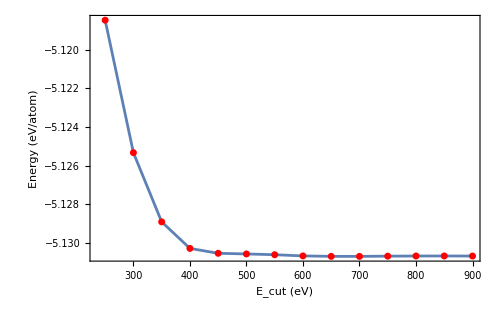

```mathematica
datasi//ListPlot[#,
Frame->True,
FrameLabel->{"E_cut (eV)", "Energy (eV/atom)"},
ImageSize->500,
Joined->True,
PlotRange->All,
InterpolationOrder->1,
Epilog->{Red,AbsolutePointSize[5],Point[#]},
BaseStyle->{FontSize->19, FontFamily->"Helvetica"}]&
```

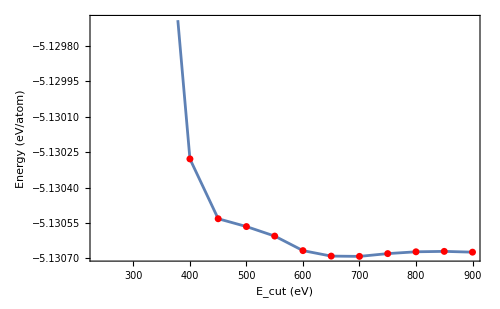

```mathematica
datasi//ListPlot[#,
Frame->True,
FrameLabel->{"E_cut (eV)", "Energy (eV/atom)"},
ImageSize->500,
Joined->True,
PlotRange->{datasi[[10,2]],datasi[[10,2]]+10^-3},
InterpolationOrder->1,
Epilog->{Red,AbsolutePointSize[5],Point[#]},
BaseStyle->{FontSize->19, FontFamily->"Helvetica"}]&
```

### The Kpoints grid convergency

```mathematica
datakp=Import["kps.dat"][[All,{1,2}]]//Map[#/{1,2}&,#]&
```

{{8,-5.13041},{9,-5.13028},{10,-5.13452},{11,-5.13425},{12,-5.13512},{13,-5.13391},{14,-5.13295},{15,-5.13388},{16,-5.13376},{17,-5.13333},{18,-5.13367},{19,-5.13347}}

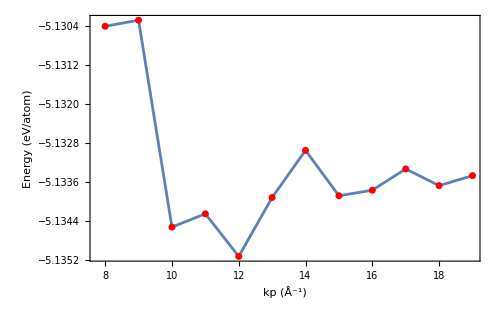

```mathematica
datakp//ListPlot[#,
Frame->True,
FrameLabel->{"kp (Å^-1)", "Energy (eV/atom)"},
ImageSize->500,
Joined->True,
PlotRange->All,
InterpolationOrder->1,
Epilog->{Red,AbsolutePointSize[5],Point[#]},
BaseStyle->{FontSize->19, FontFamily->"Helvetica"}]&
```

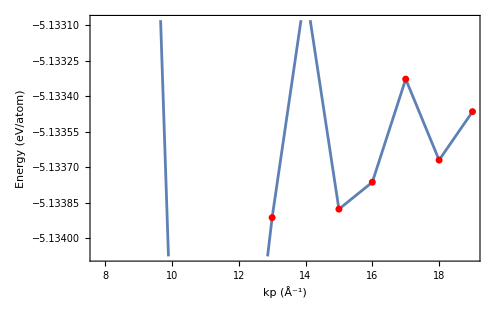

```mathematica
datakp//ListPlot[#,
Frame->True,
FrameLabel->{"kp (Å^-1)", "Energy (eV/atom)"},
ImageSize->500,
Joined->True,
PlotRange->{datakp[[8,2]]-0.2 10^-3,datakp[[8,2]]-0.2 10^-3+10^-3},
InterpolationOrder->1,
Epilog->{Red,AbsolutePointSize[5],Point[#]},
BaseStyle->{FontSize->19, FontFamily->"Helvetica"}]&
```

### EOS

```mathematica
cell=Import["cell.dat"][[All,{1,2}]]
```

{{27.67,-10.1456},{28.17,-10.1851},{28.67,-10.216},{29.17,-10.2389},{29.67,-10.2546},{30.17,-10.2636},{30.67,-10.2667},{31.17,-10.2642},{31.67,-10.2567},{32.17,-10.2446},{32.67,-10.2284},{33.17,-10.2084},{33.67,-10.1849},{34.17,-10.1583},{34.67,-10.1288},{27.67,-10.1456},{28.17,-10.1851},{28.67,-10.216},{29.17,-10.2389},{29.67,-10.2546},{30.17,-10.2636},{30.67,-10.2667},{31.17,-10.2642},{31.67,-10.2567},{32.17,-10.2446},{32.67,-10.2284},{33.17,-10.2084},{33.67,-10.1849},{34.17,-10.1583},{34.67,-10.1288}}

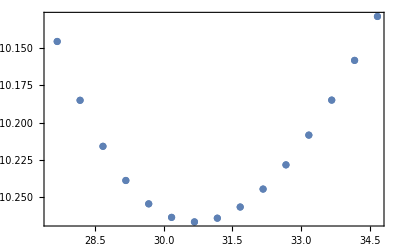

```mathematica
cell//ListPlot[#,Frame->True]&
```

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
parameters=Table[k[i],{i,4}];
nlm=NonlinearModelFit[cell,model,parameters,v]
```

FittedModel[…]

```mathematica
nlm[v]
```

5.40245+7073.4/v^2+62.2056/v^(4/3)-233.555/v^(2/3)

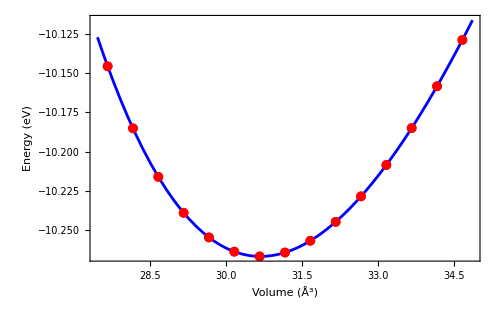

```mathematica
Plot[nlm[v],{v,(cell[[All,1]]//Min)-0.2, (cell[[All,1]]//Max)+0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)", "Energy (eV)"},
PlotStyle->{AbsoluteThickness[2], Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cell]}]
```

```mathematica
sol=Solve[{
e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],
63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],
-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlm["BestFitParameters"],{e0,B0,B',v0}]
```

{{e0→-10.2666,B0→0.671412,B'→4.64805,v0→30.6881}}

```mathematica
B0/.sol[[1]]//UnitConvert[Quantity[#,"Electronvolts"/("Angstroms")^3],"Gigapascals"]&
```

107.572 GPa

### PDOS

```mathematica
input=Import["DOSCAR-bulk","Table"];
```

```mathematica
dos=input[[7;;7+300]][[All,{1,2}]];
```

```mathematica
ef=input[[6,4]]
```

9.06454

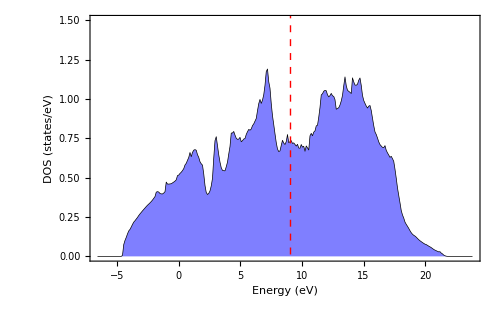

```mathematica
ListPlot[dos,
Joined->True,
Axes->False,
Frame->True,
FrameLabel->{"Energy (eV)", "DOS (states/eV)"},
GridLines->{{ef}, None},
GridLinesStyle->Directive[Red, Dashed, AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
ImageSize->500,
PlotRange->{All, {0,1.5}}]
```

Here we are going to analyze de PDOS, the arrange of the data PDOS is according to the AO:
energy,  s,  p_y p_z p_x d_{xy} d_{yz} d_{z2-r2} d_{xz} d_{x2-y2}

```mathematica
dos1=input[[7+300+2;;7+300+2+300]];
dos2=input[[7+300+2+300+2;;7+300+2+300+2+300]];
```

```mathematica
dosall=(dos1+dos2)//Map[#/{2,1,1,1,1,1,1,1,1,1}&,#]&;
```

```mathematica
f[total]=Map[{#[[1]],Plus@@(#[[2;;10]])}&,#]&;
f[s]=Map[{#[[1]],#[[2]]}&,#]&;
f[p]=Map[{#[[1]],Plus@@(#[[3;;5]])}&,#]&;
f[d]=Map[{#[[1]],Plus@@(#[[6;;10]])}&,#]&;
f[py]=Map[{#[[1]],#[[3]]}&,#]&;
f[pz]=Map[{#[[1]],#[[4]]}&,#]&;
f[px]=Map[{#[[1]],#[[5]]}&,#]&;
```

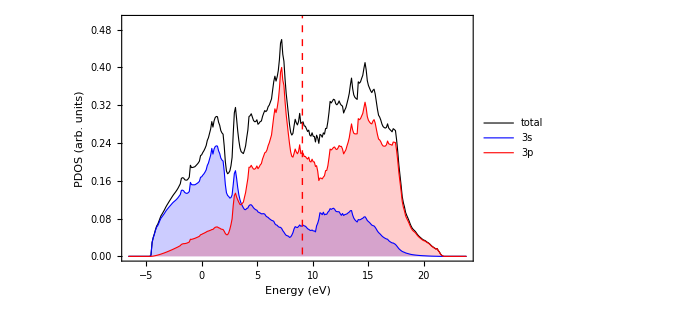

```mathematica
{dosall//f[total],dosall//f[s],dosall//f[p]}//ListPlot[#,
Joined->True,
GridLines->{{ef},None},
Filling->{2->Axis,3->Axis},
Frame->True,
FrameLabel->{"Energy (eV)","PDOS (arb. units)"},
PlotRange->{Automatic,{0,0.5}},
PlotLegends->Placed[{"total","3s","3p"},{Scaled[{0,0.75}],{0,0.5}}],
ImageSize->500,
Axes->False,
GridLinesStyle->Directive[Red,Dashed, AbsoluteThickness[1]],
PlotStyle->{{AbsoluteThickness[0.8],Black},{AbsoluteThickness[0.8],Blue},{AbsoluteThickness[0.8],Red}},
BaseStyle->{FontFamily->"Helvetica",FontSize->18}]&
```

### Visualization of Charge density

### Symm 227 (fcc) VS Symm 141

```mathematica
E227=-10.84807047;
```

```mathematica
EOS227[v_]:=13.594266553993483+2113.2192245466526/v^2+3088.718244402564/v^(4/3)-565.2716925710312/v^(2/3)-E227
```

```mathematica
EOS141[v_]:=8.792101925111997+3930.367598486751/v^2+1035.31941470454/v^(4/3)-333.3452547582743/v^(2/3)-E227
```

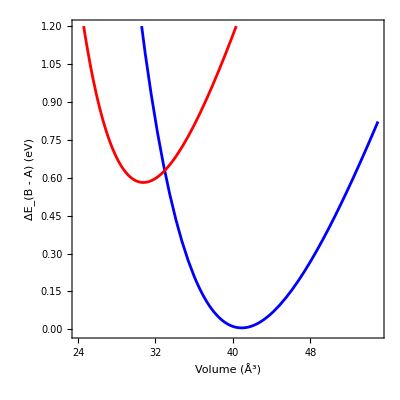

```mathematica
Plot[{EOS227[v],EOS141[v]},{v,24,55},
Frame->True,
FrameLabel->{"Volume (Å^3)","ΔE_(B - A) (eV)"},
PlotRange->{-0.01,1.2},
AspectRatio->1,
PlotStyle->{Blue,Red}]
```

```mathematica
sol=FindRoot[{D[EOS141[v2],v2]==D[EOS227[v1],v1]==(EOS141[v2]-EOS227[v1])/(v2-v1)},{{v1,38},{v2,26}}]
```

{v1→37.3739,v2→28.4833}

```mathematica
m=D[EOS141[v2],v2]/.sol
```

-0.0607759

```mathematica
D[EOS227[v1],v1]/.sol
```

-0.0607759

```mathematica
UnitConvert[Quantity[m,"Electronvolts"/("Angstroms")^3],"Gigapascals"]
```

-9.73738 GPa

```mathematica
line=Solve[(y-EOS227[v1])/(v-v1)==m/.sol,y]//FullSimplify
```

{{y→2.37677-0.0607759 v}}

```mathematica
Plot[
{Callout[EOS227[v],"Sym A=?", {50,0.8}],
Callout[EOS141[v],"Sym B=?",{39,0.6}],
y/.line[[1]]},{v,24,55},
Frame->True,
FrameLabel->{"Volume (Å^3)", "ΔE_(B - A) (eV)"},
PlotRange->{-0.01,1.2},
AspectRatio->1,
Epilog->{Green,AbsolutePointSize[6], Point[{{v1,EOS227[v1]},{v2,EOS141[v2]}}/.sol]},
PlotStyle->{Blue,Red,Black},
BaseStyle->{FontFamily->"Helvetica", FontSize->18}]
```

-Graphics-

## Part 7 : The NiO oxide

```mathematica
wrkdir="/home/qap/wrk/part7_nio";
SetDirectory[wrkdir];
```

### Non magnetic NM phase

```mathematica
cellnm=Import["cell-nm.dat"][[All,{1,2}]]
```

{{33.5,-22.5868},{34.,-22.6361},{34.5,-22.673},{35.,-22.6986},{35.5,-22.7136},{36.,-22.7188},{36.5,-22.715},{37.,-22.7028},{37.5,-22.6829},{38.,-22.6558},{38.5,-22.6222},{39.,-22.5824},{36.031,-22.7189}}

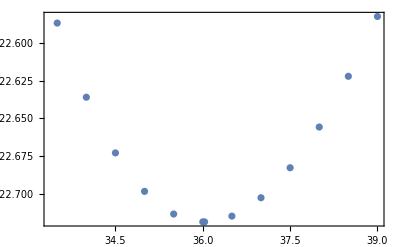

```mathematica
cellnm//ListPlot[#,Frame->True]&
```

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
parameters=Table[k[i],{i,4}];
nlmNM=NonlinearModelFit[cellnm,model,parameters,v]
```

FittedModel[…]

```mathematica
nlmNM[v]
```

13.6417+20941.1/v^2+488.219/v^(4/3)-617.377/v^(2/3)

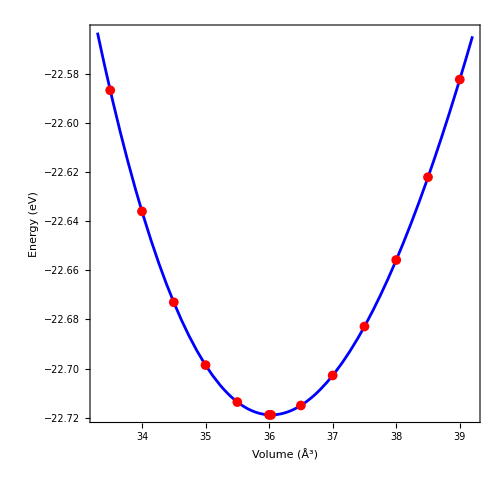

```mathematica
Plot[nlmNM[v],{v,(cellnm[[All,1]]//Min)-0.2, (cellnm[[All,1]]//Max)+0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)", "Energy (eV)"},
PlotStyle->{AbsoluteThickness[2], Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cellnm]},
AspectRatio->1]
```

```mathematica
sol=Solve[{
e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],
63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],
-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlmNM["BestFitParameters"],{e0,B0,B',v0}]
```

{{e0→-22.7188,B0→1.29488,B'→4.61456,v0→36.0324}}

```mathematica
B0/.sol[[1]]//UnitConvert[Quantity[#,"Electronvolts"/("Angstroms")^3],"Gigapascals"]&
```

207.462 GPa

### Ferromagnetic FM phase

```mathematica
cellfm=Import["cell-fm.dat"][[All,{1,2}]]
```

{{34.5,-22.6783},{35.,-22.7125},{35.5,-22.737},{36.,-22.7603},{36.5,-22.7695},{37.,-22.7729},{37.5,-22.7693},{38.,-22.7591},{38.5,-22.7425},{39.,-22.7202},{39.5,-22.6937},{40.,-22.6625},{36.986,-22.7728}}

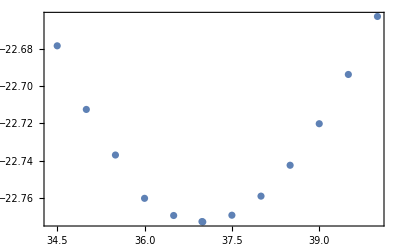

```mathematica
cellfm//ListPlot[#,Frame->True]&
```

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
parameters=Table[k[i],{i,4}];
nlmFM=NonlinearModelFit[cellfm,model,parameters,v]
```

FittedModel[…]

```mathematica
nlmFM[v]
```

27.8705-11167.5/v^2+8253.54/v^(4/3)-1215.06/v^(2/3)

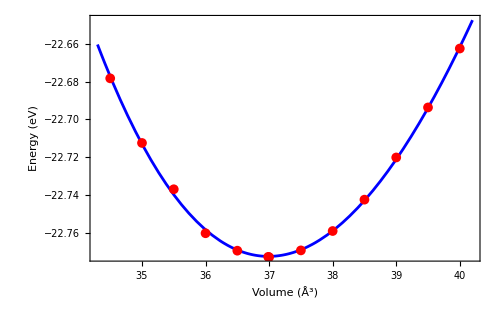

```mathematica
Plot[nlmFM[v],{v,(cellfm[[All,1]]//Min)-0.2, (cellfm[[All,1]]//Max)+0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)", "Energy (eV)"},
PlotStyle->{AbsoluteThickness[2], Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cellfm]}]
```

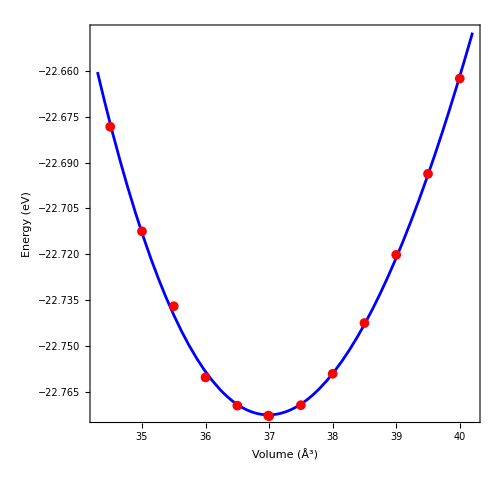

```mathematica
Plot[nlmFM[v],{v,(cellfm[[All,1]]//Min)-0.2, (cellfm[[All,1]]//Max)+0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)", "Energy (eV)"},
PlotStyle->{AbsoluteThickness[2], Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cellfm]},
AspectRatio->1]
```

```mathematica
sol=Solve[{
e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],
63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],
-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlmFM["BestFitParameters"],{e0,B0,B',v0}]
```

{{e0→147.73,B0→-192.765,B'→5.71758,v0→3.91407},{e0→-22.7725,B0→1.02084,B'→3.61575,v0→36.9903}}

```mathematica
B0/.sol[[2]]//UnitConvert[Quantity[#,"Electronvolts"/("Angstroms")^3],"Gigapascals"]&
```

163.557 GPa

### Antiferromagnetic AFM phase

```mathematica
cellafm=Import["cell-afm.dat"][[All,{1,2}]]
```

{{34.,-23.1449},{34.5,-23.1956},{35.,-23.2345},{35.5,-23.2627},{36.,-23.2809},{36.5,-23.2898},{37.,-23.29},{37.5,-23.2824},{38.,-23.2673},{38.5,-23.2454},{39.,-23.2171},{39.5,-23.183},{40.,-23.1434},{36.765,-23.2909}}

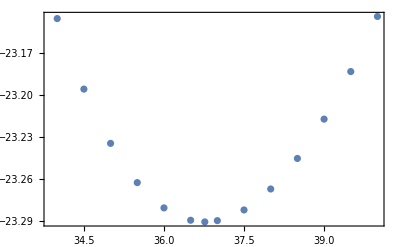

```mathematica
cellafm//ListPlot[#,Frame->True]&
```

```mathematica
model=k[1]+k[2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2;
parameters=Table[k[i],{i,4}];
nlmAFM=NonlinearModelFit[cellafm,model,parameters,v]
```

FittedModel[…]

```mathematica
nlmAFM[v]
```

12.124+19963.6/v^2+718.427/v^(4/3)-619.85/v^(2/3)

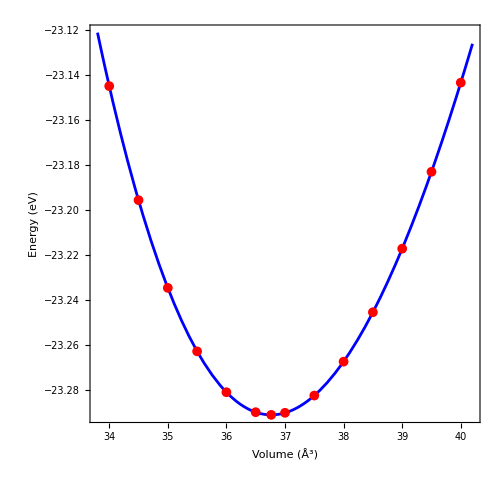

```mathematica
Plot[nlmAFM[v],{v,(cellafm[[All,1]]//Min)-0.2, (cellafm[[All,1]]//Max)+0.2},
Frame->True,
FrameLabel->{"Volume (Å^3)", "Energy (eV)"},
PlotStyle->{AbsoluteThickness[2], Blue},
Axes->None,
BaseStyle->{FontFamily->"Helvetica",FontSize->19},
ImageSize->500,
PlotRange->All,
Epilog->{AbsolutePointSize[7],Red,Point[cellafm]},
AspectRatio->1]
```

```mathematica
sol=Solve[{
e0+(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],
63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[3],
-(9 B0 v0^3)/4+9/16 B0 v0^3 B'==k[4]}/.nlmAFM["BestFitParameters"],{e0,B0,B',v0}]
```

{{e0→-23.2909,B0→1.21331,B'→4.5886,v0→36.7656}}

```mathematica
B0/.sol[[1]]//UnitConvert[Quantity[#,"Electronvolts"/("Angstroms")^3],"Gigapascals"]&
```

194.394 GPa

### DOS NM

```mathematica
dataNM=Import["DOSCAR-nm","Table"];
```

```mathematica
dosNM=dataNM[[7;;7+300]][[All,{1,2}]];
ef=dataNM[[6,4]]
```

7.96767

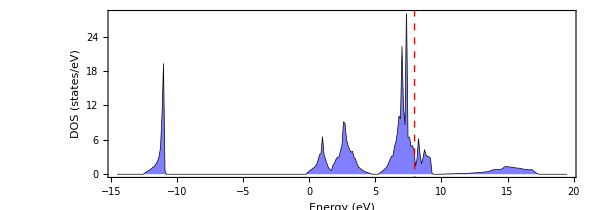

```mathematica
ListPlot[dosNM,
Joined->True,
Frame->True,
FrameLabel->{"Energy (eV)", "DOS (states/eV)"},
Axes->False,
GridLines->{{ef},None},
GridLinesStyle->Directive[Red,Dashed, AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->20},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5], Blue],
PlotStyle->{AbsoluteThickness[0.5],Black},
AspectRatio->0.35,
ImageSize->600,
PlotRange->{All,{0,28}}]
```

### DOS FM

```mathematica
dataFM=Import["DOSCAR-fm","Table"];
dosUPFM=dataFM[[7;;7+300]][[All,{1,2}]];
dosDwnFM=dataFM[[7;;7+300]][[All,{1,3}]]//Map[# {1,-1}&,#]&;

ef=dataFM[[6,4]]
```

7.64439

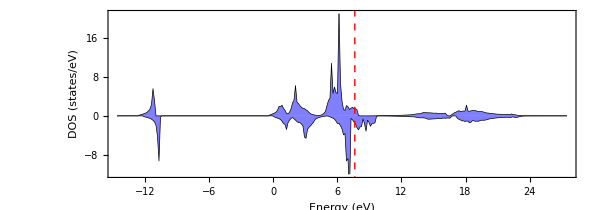

```mathematica
ListPlot[{dosUPFM,dosDwnFM},
Joined->True,
Frame->True,
FrameLabel->{"Energy (eV)", "DOS (states/eV)"},
Axes->False,
GridLines->{{ef},None},
GridLinesStyle->Directive[Red,Dashed, AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->20},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5], Blue],
PlotStyle->{{AbsoluteThickness[0.5],Black},{AbsoluteThickness[0.5],Black}},
AspectRatio->0.35,
ImageSize->600,
PlotRange->{All,{-12,21}}]
```

### DOS AFM

```mathematica
dataAFM=Import["DOSCAR-afm","Table"];
dosUPAFM=dataAFM[[7;;7+300]][[All,{1,2}]];
dosDwnAFM=dataAFM[[7;;7+300]][[All,{1,3}]]//Map[# {1,-1}&,#]&;

ef=dataAFM[[6,4]]
```

7.37541

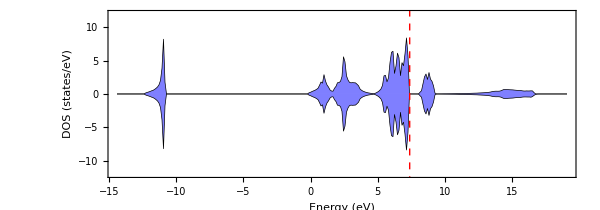

```mathematica
ListPlot[{dosUPAFM,dosDwnAFM},
Joined->True,
Frame->True,
FrameLabel->{"Energy (eV)", "DOS (states/eV)"},
Axes->False,
GridLines->{{ef},None},
GridLinesStyle->Directive[Red,Dashed, AbsoluteThickness[1]],
BaseStyle->{FontFamily->"Helvetica",FontSize->20},
Filling->Axis,
FillingStyle->Directive[Opacity[0.5], Blue],
PlotStyle->{{AbsoluteThickness[0.5],Black},{AbsoluteThickness[0.5],Black}},
AspectRatio->0.35,
ImageSize->600,
PlotRange->{All,{-12,12}}]
```